```mathematica
GetCoord[line_,split_]:=
{line[[1,1]]+split*(line[[2,1]]-line[[1,1]]),line[[1,2]]+split*(line[[2,2]]-line[[1,2]])};
SquareStacks[lineRoot_,depth_,alpha_] := Module[{i,lineList,splits,points,len},
splits=Sort[Table[RandomReal[],alpha]];
points=Table[GetCoord[lineRoot,splits[[i]]],{i,1,alpha}];
PrependTo[points,lineRoot[[1]]];
AppendTo[points,lineRoot[[2]]];
lineList={lineRoot};
For[i=1,i<=alpha+1,i++,
AppendTo[lineList,{points[[i]],{points[[i,1]]-(points[[i+1,2]]-points[[i,2]]),points[[i,2]]+points[[i+1,1]]-points[[i,1]]}}];
];
lineList
];
PlotSquares[lineList_]:=Module[{gfxList},
gfxList=Table[Graphics[Line[lineList[[i]]]],{i,1,Length[lineList]}];
Show[gfxList]
];
```

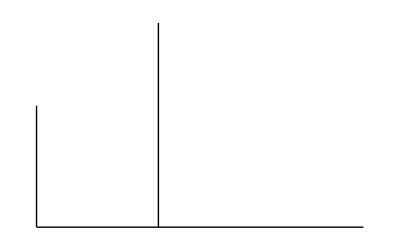

```mathematica
PlotSquares[SquareStacks[{{0,0},{1,0}},1,1]]
```